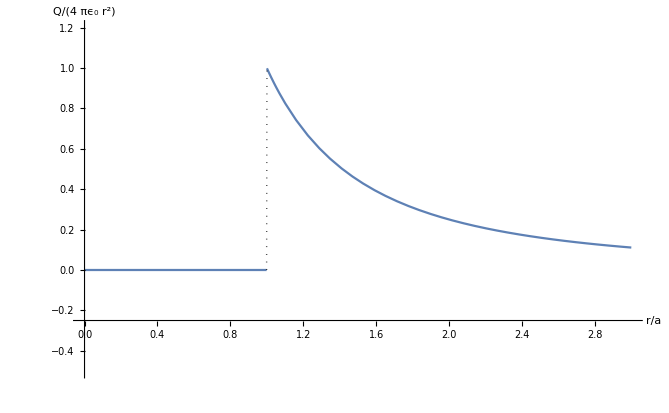

```mathematica
f[x_]:= 1/(x)^2HeavisideTheta[x-1]

Plot[f[a],{a,0,3},PlotRange->{-.5,1.2},AxesLabel-> {Style[r/a,FontFamily-> "Times New Roman",FontSize->24],Style[|E⃗|=Q/(4 Subscript[πϵ, 0] r^2),FontFamily->"Times New Roman",FontSize->24]},AxesOrigin->{0,-.25},Exclusions->a==1,ExclusionsStyle ->Dotted]
```

```mathematica
g[x_]:=x HeavisideTheta[1-x]+(1/x^2) HeavisideTheta[x-1]
```

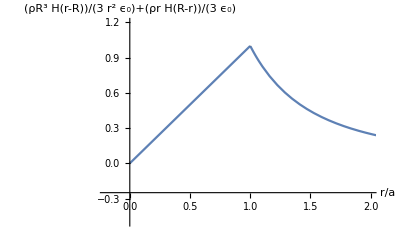

```mathematica
Plot[g[a],{a,0,3},PlotRange->{{-.2,2},{-.5,1.2}},AxesLabel-> {Style[r/a,FontFamily-> "Times New Roman",FontSize->12],Style[(ρr/(3 Subscript[ϵ, 0]))H[R-r]+(ρR^3/(3 Subscript[ϵ, 0] r^2))H[r-R],FontFamily->"Times New Roman",FontSize->12]},AxesOrigin->{0,-.25},Exclusions->a==1,ExclusionsStyle ->Dotted]
```

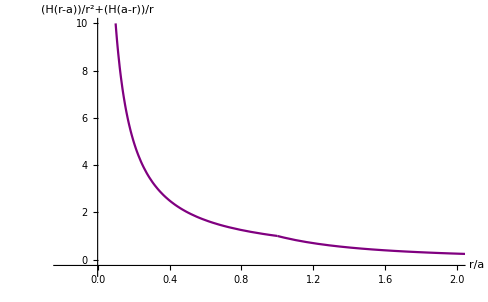
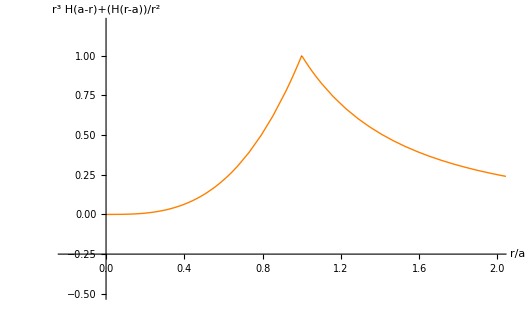

```mathematica
h[x_]:= 1/x HeavisideTheta[1-x]+ (1/x^2)HeavisideTheta[x-1]
i[x_] := x^3HeavisideTheta[1-x]+(1/x^2)HeavisideTheta[x-1]
Plot[h[a],{a,0,3},PlotRange->{{-.2,2},{-.5,10}},PlotStyle-> Purple,AxesLabel-> {Style[r/a,FontFamily-> "Times New Roman",FontSize->24],Style[(1/r)H[a-r]+(1/r^2)H[r-a],FontFamily->"Times New Roman",FontSize->16]},AxesOrigin->{0,-.25},Exclusions->a==1,ExclusionsStyle ->Dotted]Plot[i[a],{a,0,3},PlotRange->{{-.2,2},{-.5,1.2}},PlotStyle-> {Orange,Thick},AxesLabel-> {Style[r/a,FontFamily-> "Times New Roman",FontSize->24],Style[r^3 H[a-r]+(1/r^2)H[r-a],FontFamily->"Times New Roman",FontSize->16]},AxesOrigin->{0,-.25},Exclusions->a==1,ExclusionsStyle ->Dotted]
```